Hu-Sugiyama Formulas

```mathematica
Quit[]
```

```mathematica
Needs["Dodelson`TESTCommonParameters`"]
Needs["Dodelson`DodelsonDefine`"]
Needs["Dodelson`LocalFunctions`"]

RecombinationSubs
equalitySubs
ayetaSubs
SoundSubs
DefEqn886
```

General::obspkg: TraditionalForm`"Utilities`Notation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Needs::nocont: Context TraditionalForm`"Dodelson`TESTCommonParameters`" was not created when Needs was evaluated.

Needs::nocont: Context TraditionalForm`"Dodelson`DodelsonDefine`" was not created when Needs was evaluated.

Needs::nocont: Context TraditionalForm`"Dodelson`LocalFunctions`" was not created when Needs was evaluated.

subZrecomb :: z_*→1000

subarecomb :: a_*→1/(z_*+1)

subyrecomb :: y_*→(a_*)/a_eq

Some definitions referencing 'equality' point :

defkeq :: k_eq→a_eq H(a_eq)

subkeq :: k_eq→√2 √((H_0^2 Ω_m)/a_eq)

subH0 :: H_0→(√((a_eq k_eq^2)/Ω_m))/(√2)

subkkeq :: k→k_eq kk_eq

subetat :: η'(t)→1/(a(η))

subyeta :: y(η)→(a(η))/a_eq

subDyeta :: y'(η)→(a'(η))/a_eq

subHt :: H→(a'(t))/(a(t))

defaeta :: a(η_):=y(η) a_eq

subHeta :: H→(a'(η))/(a(η))^2

deffnu :: f_ν:=ρ_ν/(ρ_γ+ρ_ν)

defRhoG :: ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoRad :: ρ_r(a_):=(f_ν+1) ρ_γ(a)

defRhoM :: ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoB :: ρ_b(a_):=(Ω_b ρ_cr)/a^3

defRho :: ρ(a_):=ρ_de(a)+ρ_m(a)+ρ_r(a)

subRhoCR :: ρ_cr→(3 H_0^2)/(8 G π)

defe255 :: (∂ρ_t(t))/(∂t)+(3 (∂a_t(t))/(∂t) (𝒫_t(t)+ρ_t(t)))/(a_t(t))==0

defe255a :: (∂ρ_a(a))/(∂a)+(3 (𝒫_a(a)+ρ_a(a)))/a==0

subaeq :: a_eq→(f_ν C_γ+C_γ)/(h^2 Ω_m)

subC :: C_γ→(a_eq h^2 Ω_m)/(f_ν+1)

defHa :: Ha(a_):=√(1/3 (8 π G) ρ(a))

defetade :: η_de(a_):=∫_0^a 1/(aa^2 Ha(aa))ⅆaa

defe242 :: χ(a_):=∫_a^1 1/(aa^2 Ha(aa))ⅆaa

For backward consistency : Null

η[a_] :: (2 (√(a+a_eq)-√a_eq))/(H_0 √Ω_m)

η_* :: (2 (√(a_eq+a_*)-√a_eq))/(H_0 √Ω_m)

η_y[y_] :: (2 (√(y a_eq+a_eq)-√a_eq))/(H_0 √Ω_m)

Jacobian dη/dy => a_eq/(H_0 √(a_eq (y+1)) √Ω_m)
Or  -> dη/dy = (√2)/(k_eq √(y+1))

y[η_] :: 1/8 k_eq η (k_eq η+4 √2)

Useful relationships: From the definitions: dη==dt/a  and  H=((∂a(t))/(∂t))/(a(t)) => a H==(∂a(t))/(∂t) => dt==da/(a H) => dη==da/(a^2 H)

defR :: R(a_):=(3 ρ_m(a))/(4 ρ_γ(a))

defReta :: R_η(η_):=(3 ρ_m(y(η) a_eq))/(4 ρ_γ(y(η) a_eq))

Eqn819 :: c_s(a_):=√(1/(3 (R(a)+1)))

Eqn819eta :: c_s(eta_):=√(1/(3 (R_η(eta)+1)))

Eqn822 :: r_s(η_):=∫_0^η c_s(ep)ⅆep

c_s(eta_):=√(1/(3 (R_η(eta)+1))) => 1/(√3 √(3/32 (f_ν+1) k_eq η (k_eq η+4 √2)+1))Null

r_s[η_] :: -(4 √2 log((6 √2 (f_ν+1)+4 √6 √(f_ν+1))/(3 (f_ν+1) (k_eq η+2 √2)+√3 √((f_ν+1) (3 (f_ν+1) k_eq η (k_eq η+4 √2)+32)))))/(3 √(f_ν+1) k_eq)

#### Correspondence with Eqn.7.32 : Φls, large-scale solution. Show difference factor.

```mathematica
eA6:=Subscript[U, G][a]->(a^3+2/9 a^2-8/9 a-16/9+16/9 √(a+1))/(a(a+1))
factorA6=Φls[a]/eA6[[2]]//Simplify
```

(9 (a+1) Φ(0))/(10 a^2)

#### Correspondence with Eqn.8.87 :

```mathematica
eA12:=Subscript[N, 2][a_]->-1/10(20 a+19)/(3 a+4)A Subscript[U, G][a]-8/3 a/(3 a+4)A+8/9 Log[(3 a+4)/4]A
eA12
eA12/.Subscript[U, G][a]->Φls/factorA6
subN2=Collect[%,A]
```

N_2(a_)→8/9 log(1/4 (3 a+4)) A-((20 a+19) U_G(a) A)/(10 (3 a+4))-(8 a A)/(3 (3 a+4))

N_2(a_)→-((20 a+19) A Φls a^2)/(9 (a+1) (3 a+4) Φ(0))-(8 A a)/(3 (3 a+4))+8/9 A log(1/4 (3 a+4))

N_2(a_)→A (-((20 a+19) Φls a^2)/(9 (a+1) (3 a+4) Φ(0))-(8 a)/(3 (3 a+4))+8/9 log(1/4 (3 a+4)))

#### Correspondence to Eqn.8.87 : we see that the 0.48 factor is .05328 if f_νis choosen to yield the 1.16 constant.

```mathematica
eA16=Subscript[Δ, T.HS][a_]->(1+2/5 Subscript[f, ν](1-.333 a/(a+1)))A Subscript[U, G][a]
tmp=eA16[[2]]/.a->0/.A->1/.Subscript[U, G][_]->1 (* What is Subscript[f, ν]? *)
subf=Solve[tmp==1.16,Subscript[f, ν]][[1]]
Collect[eA16,A Subscript[U, G][a]]
subDelta=%/.Subscript[U, G][a]->Φls/factorA6
```

Δ_(T.HS)(a_)→A (2/5 (1-(0.333 a)/(a+1)) f_ν+1) U_G(a)

(2 f_ν)/5+1

{f_ν→0.4}

Δ_(T.HS)(a_)→A (2/5 (1-(0.333 a)/(a+1)) f_ν+1) U_G(a)

Δ_(T.HS)(a_)→(10 a^2 A (2/5 (1-(0.333 a)/(a+1)) f_ν+1) Φls)/(9 (a+1) Φ(0))

```mathematica
eA20=Φ[0,k]^2==(5/6(1+2/5 Subscript[f, ν]))^2(Subscript[k, eq]/k)^4 A[k]^2
subA=Solve[eA20,A[k]][[2]]
```

(Φ(0,k))^2==(25 ((2 f_ν)/5+1)^2 k_eq^4 (A(k))^2)/(36 k^4)

{A(k)→(6 k^2 Φ(0,k))/((2 f_ν+5) k_eq^2)}

#### Check f_νwith A17 => a difference of .64 <=>.65

```mathematica
8/5 Subscript[f, ν]/.subf
```

0.64

#### Corresponding equation for Φbar and Ψbar. We see that the references to Φls need a factor of Φ[0] and Ψbar and Φbar need a overall factor of A. (Eqn.A17 H-S)

```mathematica
ΦbarHS[kkeq_,y_]:=3/4(1/kkeq)^2(y+1)/y^2 Subscript[Δ, T.HS][y];
ΨbarHS[kkeq_,y_]:=-3/4(1/kkeq)^2(y+1)/y^2(Subscript[Δ, T.HS][y]+.65 Subscript[N, 2][y]/(1+y));
PhiBar=HoldForm[ΦbarHS[kkeq,y]]->ΦbarHS[kkeq,y]/.subDelta

PsiBar=HoldForm[ΨbarHS[kkeq,y]]->ΨbarHS[kkeq,y]/.subDelta/.subN2//Simplify;
PsiBar=Collect[%,{Φls,Φ[0]}]
```

ΦbarHS(kkeq,y)→(5 A (2/5 f_ν (1-(0.333 y)/(y+1))+1) Φls)/(6 kkeq^2 Φ(0))

ΨbarHS(kkeq,y)→(A ((-0.667 f_ν-2.5) y^4+(-1.88933 f_ν-4.75) y^3-1.33333 f_ν y^2-2.30417 y^2) Φls)/(kkeq^2 y^2 (y+1.) (3. y+4.) Φ(0))+(A (1.3 y^2+1.3 y-1.3 (y+1.) (y+1.33333) log(0.75 y+1.)))/(kkeq^2 y^2 (y+1.) (3. y+4.))

#### The PsiBar and PhiBar term have the Φ_ls term which causes problems with the integration even though it is nicely behaved at y->0 (see plot below.). We investigate the behavior of Φ_ls. A function PhiLS is defined to switch between the series approximation and the full equation. Note that Φ[0] is factored out.

(9 y^3+2 y^2-8 y+16 √(y+1)-16)/(10 y^3)

(33 y^4)/1280-(21 y^3)/640+(7 y^2)/160-y/16+1

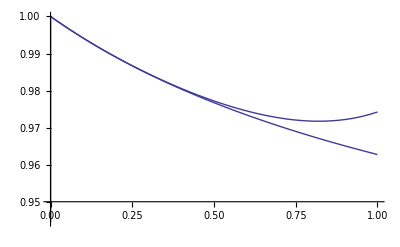

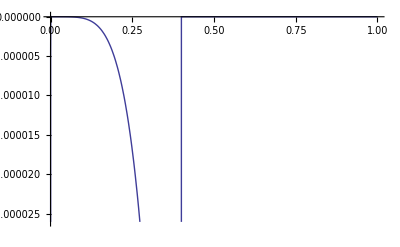

```mathematica
PhiLSX=Φls[y]/Φ[0]
PhiSeriesX=Series[PhiLSX,{y,0,4}]//Normal
Plot[{PhiLSX,PhiSeriesX}/.y->yy,{yy,0,1}]
Clear[PhiSeries,PhiLS]
PhiSeries[yy_]:=PhiSeriesX/.y->yy;
PhiOrig[yy_]:=PhiLSX/.y->yy;
PhiLS[y_]:=If[y>.4,PhiOrig[y],PhiSeries[y]];
Plot[{(PhiLSX/.y->yy)-PhiLS[yy]},{yy,0,1},PlotRange->Automatic]
```

#### Using above PhiLS function we assemble an expression for the integrand term, Φ- Ψ of Eqn.8.24 or H-S.D6, useful for numerical solutions. Set Ω_m:=.15/h^2.

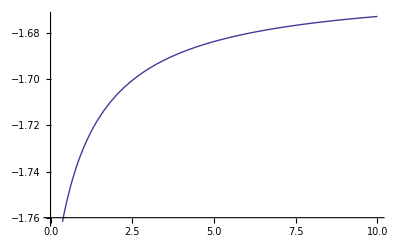

-1.15123

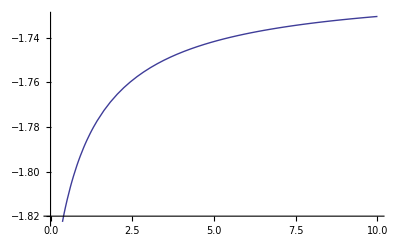

-1.

(A ((-0.667 f_ν-2.5) y^4+(-1.88933 f_ν-4.75) y^3-1.33333 f_ν y^2-2.30417 y^2))/(kkeq^2 y^2 (y+1.) (3. y+4.))-(5 A (2/5 f_ν (1-(0.333 y)/(y+1))+1))/(6 kkeq^2)+(A (1.3 y^2+1.3 y-1.3 (y+1.) (y+1.33333) log(0.75 y+1.)))/(kkeq^2 y^2 (y+1.) (3. y+4.))

-1.86061/kkeq^2

```mathematica
Clear[Subscript[Ω, m]]
subOm:=Subscript[Ω, m]->.15/h^2;
subk:=Subscript[k, eq]->(Subscript[k, eq]//NumericalValues);
suby:=y->(y[eta]//NumericalValues)
subAa:=subA/.A[k]->A/.Φ[0,k]->Φ[0]/.subf

PsiBar[[2]]-PhiBar[[2]];
PsiMinusPhi[yy_,Xkkeq_]:=(PsiBar[[2]]-PhiBar[[2]])/.y->yy/.kkeq->Xkkeq/.Φls->PhiLS[yy] Φ[0]
pmp=(PsiMinusPhi[Y,1]/.A->1)//.subf//.subOm;
(** PLOT **)
Plot[pmp/.Y->y,{y,0,10}]
Limit[pmp,Y->10^-15] (* 1/y^2 limit *)

pmp=PsiMinusPhi[y[η],k/Subscript[k, eq]]/.subAa//.subf/.Φ[0]->1/.subk;
Plot[pmp/.η->(Subscript[η, y][y]//NumericalValues),{y,0,10}]
Limit[pmp,η->10^-15]

pmp=(PsiBar[[2]]-PhiBar[[2]])/.Φls->Φ[0]
Limit[pmp,y->10^-15]/.A->1/.subf
(* It appears that there is substantial numerical truncation near y==0 *)
```

#### Transform integrand to use ΨminusΦ.

```mathematica
(* transform e824 into HS-D6 *)
DefEqn824;
hold824=hold824/.Integrate->XIntegrate
hold824//ReleaseHold;
e824a=e824/.kkeq->k/Subscript[k, eq]/.Subscript[k, eq]->1(* eliminate kkeq in e824 *)
e824b=e824a/.Equal->Rule;
sub824=e824b;
ThetaPhi[kX_,ηX_]:=e824a[[2]]/.k->kX/.η->ηX/.Subscript[r,s][a_]->RS[a]/.RS[a_]->Subscript[r, s][a] ;
ThetaPhi[kX,ηX]
"This is HS-D6 with r_s replacement."
```

e824=Φ(kkeq,η)+Θ_0(kkeq,η)==XIntegrate(integrand824(η,eta,kkeq),{eta,0,η})+cos(k_eq kkeq r_s(η)) (Φ(0)+Θ_0(0))

Θ_0(k,η)+Φ(k,η)==XIntegrate(integrand824(η,eta,k),{eta,0,η})+cos(k r_s(η)) (Θ_0(0)+Φ(0))

XIntegrate(integrand824(ηX,eta,kX),{eta,0,ηX})+cos((4 √2 kX log((6 √2 (f_ν+1)+4 √6 √(f_ν+1))/(3 (f_ν+1) (k_eq ηX+2 √2)+√3 √((f_ν+1) (3 (f_ν+1) k_eq ηX (k_eq ηX+4 √2)+32)))))/(3 √(f_ν+1) k_eq)) (Θ_0(0)+Φ(0))

This is HS-D6 with r_s replacement.

(k sin(k (r_s(η)-r_s(eta))) (Φ(k/k_eq,eta)-Ψ(k/k_eq,eta)))/(√3)

-(k sin(k (r_s(η)-r_s(eta))) ΨminusΦ(y,k))/(√3)

DEBUG

-1.71735

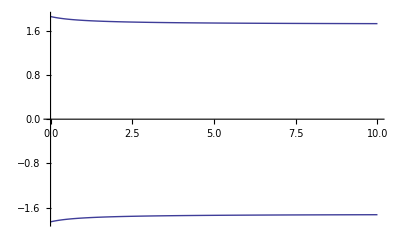

In above, the coefficient of Sin in the integrand seems  OK

```mathematica
Map[Clear,{eta,k,Xeta,Xη,Xk}];
holdint824//ReleaseHold;
integrand824[η,eta,k/Subscript[k, eq]]
int824a=integrand824[η,eta,k/Subscript[k, eq]]/.Subscript[k, eq]->1/.Φ(k,eta)-Ψ(k,eta)->-ΨminusΦ[y,k]
int824b=int824a/.ΨminusΦ[y,k]->PsiMinusPhi[y,k/Subscript[k, eq]]/.subAa/.subf/.Φ[0]->1/.suby/.subk;
int824c=int824b/.Subscript[r,s][a_]->RS[a]/.RS[a_]->Subscript[r, s][a] (* PROBLEM with Subscript *);
int824c=int824c//NumericalValues;

(****)
"
StyleBox[\"DEBUG\",\nFontColor->RGBColor[1, 0, 0]]"

pmp=PsiMinusPhi[y[eta],k/Subscript[k, eq]]/.subAa/.subf/.Φ[0]->1/.subk;
pmp1=PsiMinusPhi[y,k/Subscript[k, eq]]/.subAa/.subf/.Φ[0]->1/.suby/.subk;
pmp1/.eta->Subscript[η, 0]//NumericalValues
pmp2=int824c/.Sin[a_]->1/.k->√3;
Plot[{pmp,pmp2}/.eta->(Subscript[η, y][y]//NumericalValues),{y,0,10}]
"In above, the coefficient of Sin in the integrand seems  consistent with PsiMinusPhi function."
```

#### We numerically evaluate the integral in Eq. 8.24. Plot of integrand and Eq.8.24 is presented.

```mathematica
Map[Clear,{integrand824,Xeta,Xη,Xk}];
integrand824[Xη_,Xeta_,Xk_]:= int824c/.η->Xη/.eta->Xeta/.k->Xk;
i824[η_,k_]:=NIntegrate[integrand824[η,eta,k],{eta,0,η}];
XXηstar=η[SubStar[a]]/.subrhocr/.subH0//NumericalValues
```

Clear::ssym: TraditionalForm`6.319678506611356`*^-16 is not a symbol or a string.

4.7722×10^16

```mathematica
XXeta=  XXηstar
XXη0=η[Subscript[a, 0]]/.subrhocr/.subH0//NumericalValues
int824c/.η->XXeta/.k->XXk/.eta->etap;
kmax=1200/XXηstar
"The integral upper limit is: "
kmax XXηstar /√3
```

4.7722×10^16

4.80991×10^18

2.51456×10^-14

The integral upper limit is:

692.82

```mathematica
XXk=430/XXη0;
Plot[  int824c/.η->XXeta/.k->XXk/.eta->etap,{etap,0,XXeta }   ]
Plot[  i824[  XXeta ,  XXk =X/XXη0  ],{X,1,1200}  ]
"Is plot of i824 accurate?  It's magnitude seems too large, and contributes to the difference in the Figures.  The numerical integration may be the problem. "
```

-Graphics-

Try change of integration variables to reduce round-off errors.

2.73562×10^-16

1.57185×10^18

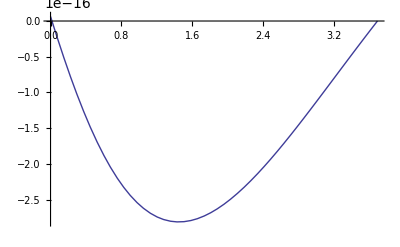

-Graphics-

-Graphics-

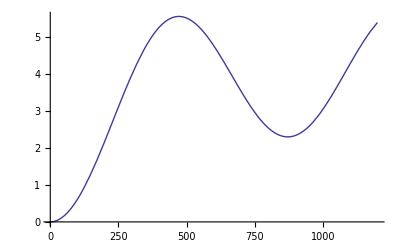

Make no significant difference.

```mathematica
"Try change of integration variables to reduce potential truncation errors."
PsiMinusPhi[y,k/Subscript[k, eq]];
PmP=Collect[%,{k,Subscript[k, eq]}];
int824d=int824a/.ΨminusΦ[y,k]->PmP/.subAa/.subf/.Φ[0]->1/.y->(y[η]/.η->keqη/Subscript[k, eq]);
int824d=int824d/.Subscript[r,s][a_]->RS[a]/.RS[a_]->Subscript[r, s][a] ;
int824d=int824d/.η->keqη/Subscript[k, eq]/.eta->keqeta/Subscript[k, eq];
int824d=int824d/.subf/.k->kkeq Subscript[k, eq]//Simplify;
int824d=int824d/.subk;
XXk=430/XXη0 (* first zero point*)
XXeta=  XXηstar  ;
XXη0=η[Subscript[a, 0]]/.subrhocr/.subH0//NumericalValues
int824e=int824d/.keqeta->(XXηstar Subscript[k, eq]/.subk)/.kkeq->(XXk/Subscript[k, eq]/.subk)/.keqη->keqetap;
Plot[  int824e,  {keqetap,0,(XXηstar Subscript[k, eq])/.subk }   ]

integrand824[Xη_,Xeta_,Xk_]:=
 int824d/.keqeta->(Xeta Subscript[k, eq]/.subk)/.kkeq->(Xk/Subscript[k, eq]/.subk)/.keqη->(Xη Subscript[k, eq]/.subk);
integrand824[Xη,Xeta,Xk];
Plot[  int824c/.η->XXeta/.k->XXk/.eta->etap,{etap,0,XXeta }   ]
Plot[  integrand824[etap,XXηstar,XXk],  {etap,0,XXηstar }   ]

i824[η_,k_]:=NIntegrate[integrand824[η,eta,k],{eta,0,η}];
Plot[  i824[  XXeta ,  XXk =X/XXη0  ],{X,1,1200}  ]
"Makes no significant difference."
```

3/2 cos(1.36765×10^16 k log(23.4725/(4.2 (1.16524×10^-16 η+2 √2)+2.04939 √(4.894×10^-16 (1.16524×10^-16 η+4 √2) η+32))))

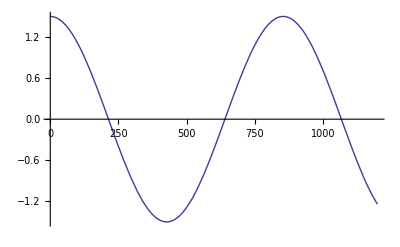

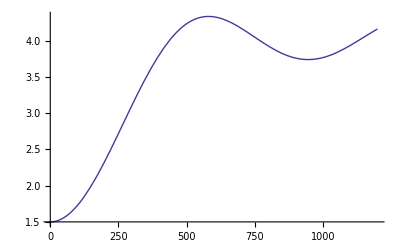

I think this should be Fig 4.

```mathematica
ThetaPhi[kX_,ηX_]:=e824a[[2]]/.k->kX/.η->ηX/.Subscript[r,s][a_]->RS[a]/.RS[a_]->Subscript[r, s][a] ;
ThetaPhi[kX,ηX];

ThetaPhi[k,η]/.Subscript[Θ, 0][0]->Φ[0]/2;
TP=%/.subf/.Φ[0]->1/.subk;
TP[[1]]

Plot[  TP[[1]]/.η->XXeta/.k->X/XXη0/.XIntegrate->NIntegrate,{X,1,1200}]
Plot[  TP     /.η->XXeta/.k->X/XXη0/.XIntegrate->NIntegrate,{X,1,1200}]
"I think this should be Fig 4."
```

Plot H-S Fig.1.  Do we get a good approximation to Fig 1 by only using the cos[k r_s] term?

6.31968×10^-16

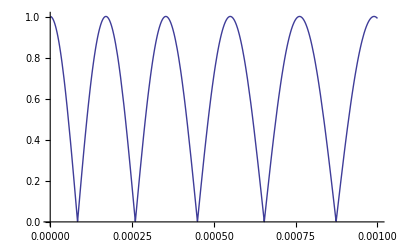

It appears that the k r_s values are similar and that the cos term is the major contributor to the graph values.

Let's look at integral term again.

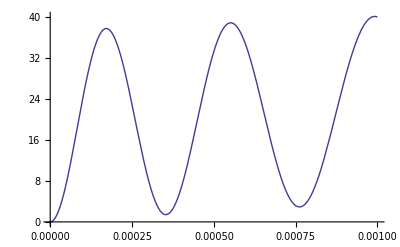

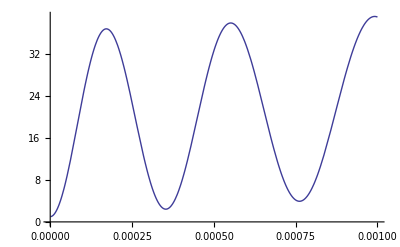

```mathematica
"Plot H-S Fig.1.  Do we get a good approximation to Fig 1 by only using the cos[k r_s] term? "
Subscript[Ω, m]:=.06
h:=.5
kfig1:=0.065 sec2Mpc//NumericalValues
kfig1
Plot[Abs[Cos[kfig1  Subscript[r, s][η[a]]/.subf//NumericalValues]]+.001,{a,10^-6,.001}]
"It appears that the k r_s values are similar and that the cos term is the major contributor to the graph values."
"Let's look at integral term again."
i824[η_,k_]:=NIntegrate[integrand824[η,eta,k],{eta,0,η}]
Plot[i824[η[a]/.subf//NumericalValues,kfig1],{a,10^-6,.001}]
Plot[Cos[kfig1  Subscript[r, s][η[a]]/.subf//NumericalValues]+  i824[η[a]/.subf//NumericalValues,kfig1],{a,10^-6,.001}]
```

6.31968×10^-16

5.04681×10^18 (√(b+0.00231327)-0.0480965)

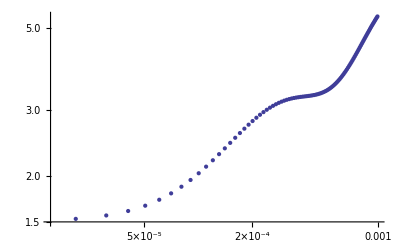

```mathematica
Map[Clear,{eta}];
Xk=.065 sec2Mpc//NumericalValues
eta[a_]:=η[a]//NumericalValues
eta[b]
table=Table[{a,Abs[TP/.η->eta[a]/.k->Xk/.XIntegrate->NIntegrate]},{a,10^-6,.001,10^-5}];
ListLogLogPlot[table]
```